```mathematica
paramvals={v->1,dstep->8,fs->5,w->2,fd->4,a->1.07,b->.186,ϵ0->.7};
```

## Stepping rate

rate from my definition

```mathematica
kstep[f_]:=Piecewise[{{v/dstep (1-(f/fs)^w),0<f<fs},{0,f≥fs},{v/dstep,f<0}}]
```

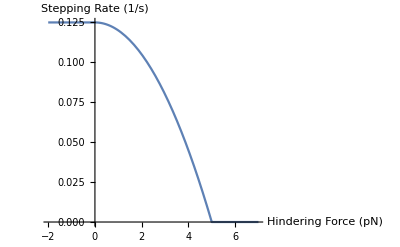

```mathematica
Plot[kstep[f]/.paramvals,{f,-2,7},AxesLabel->{"Hindering Force (pN)","Stepping Rate (1/s)"}]
```

translate to velocity

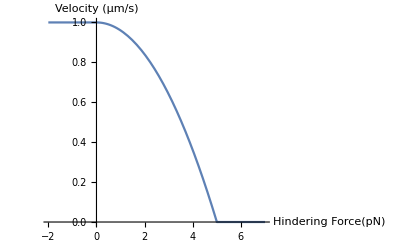

```mathematica
myvel=Plot[dstep*kstep[f]/.paramvals,{f,-2,7},AxesLabel->{"Hindering Force(pN)","Velocity (μm/s)"}]
myvelnm=Plot[1000*dstep*kstep[f]/.paramvals,{f,-2,7},AxesLabel->{"Hindering Force(pN)","Velocity (μm/s)"}];
```

## Run Length

My off rate

```mathematica
koff[f_]:=Piecewise[{{ϵ0 Exp[Abs[f]/fd],f≤fs},{a+b f,f>fs}}]
```

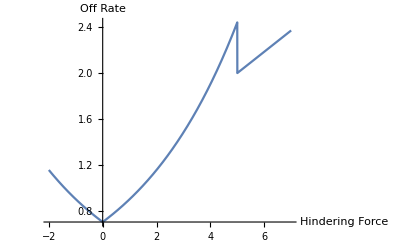

```mathematica
mykoff=Plot[koff[f]/.paramvals,{f,-2,7},AxesLabel->{"Hindering Force","Off Rate"}]
```

Then my run length is

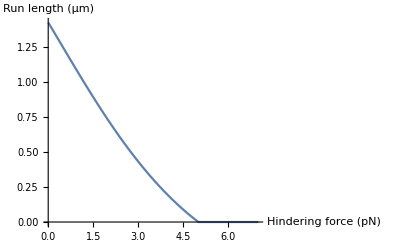

```mathematica
myrl=Plot[(dstep kstep[f])/koff[f]/.paramvals,{f,0,7},AxesLabel->{"Hindering force (pN)","Run length (μm)"}]
myrlnm=Plot[1000*(dstep kstep[f])/koff[f]/.paramvals,{f,0,7},AxesLabel->{"Hindering force (pN)","Run length (nm)"}];
```

## From Kunwar 2008 / Schnitzer 2000

Ambarish takes his run lengths and velocities from Schnizter 2000.  For velocity, we have

```mathematica
v[f_]:=(kcat d (1-(f/f0)^2)) c/(c+(kcat+koff0 Exp[f dl /(kB T)])/kon)
```

The fit for run length is given as

```mathematica
L[f_]:=d c a Exp[-f δl/(kB T)]/(c+b(1+a Exp[-f δl/(kB T)]))
```

with the parameters

```mathematica
k2008params={d->Quantity[8,"Nanometers"],δl->Quantity[1.3,"Nanometers"],b->Quantity[.029,"Micromolar"],a->107,kB->Quantity["BoltzmannConstant"],c->Quantity[3,"Millimolar"],T->Quantity[300,"Kelvins"],
koff0->Quantity[55,1/"Seconds"],dl->Quantity[1.6,"Nanometers"],kon->Quantity[2*^6,1/("Molar"*"Seconds")],kcat->Quantity[105,1/"Seconds"],f0->Quantity[8,"Piconewtons"]};
```

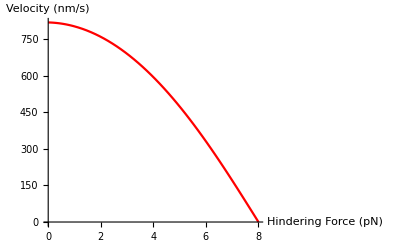

```mathematica
Svel=Plot[v[Quantity[f,"Piconewtons"]]/.k2008params,{f,0,8},PlotStyle->Red,AxesLabel->{"Hindering Force (pN)","Velocity (nm/s)"}]
```

This is quite different than mine:
my stall force is much lower
my unloaded velocity is higher

however, both are superlinear

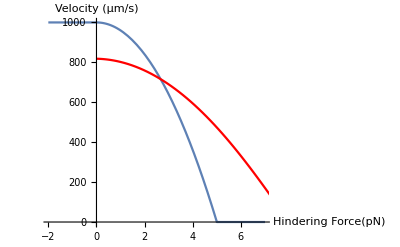

```mathematica
Show[{myvelnm,Svel}]
```

Run length as a function of force is

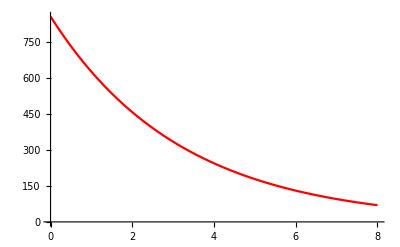

```mathematica
schnitzerrl=Plot[L[Quantity[f,"Piconewtons"]]/.k2008params,{f,0,8},PlotStyle->Red]
```

This is quite different than the run lengths in my model, for several reasons:
I put a hard stall at 5pN
My 0-force run lengths are much longer to match Michael and Jing’s results

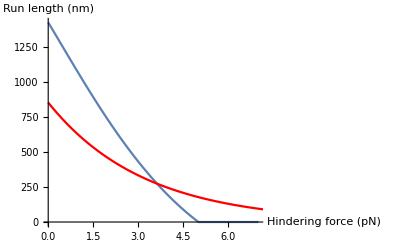

```mathematica
Show[{myrlnm,schnitzerrl}]
```

Then the effective koff is

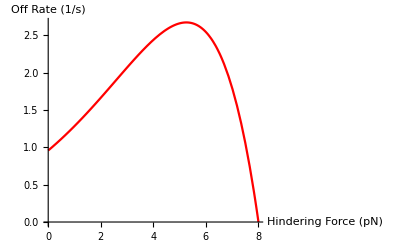

```mathematica
skoff=Plot[v[Quantity[f,"Piconewtons"]]/L[Quantity[f,"Piconewtons"]]/.k2008params,{f,0,8},AxesLabel->{"Hindering Force (pN)","Off Rate (1/s)"},PlotStyle->Red]
```

which is drastically different than mine. We’re using the off rate from Kunwar 2011 based on Gross lab measurements.

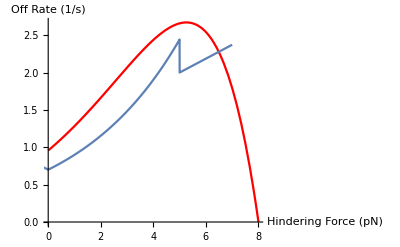

```mathematica
Show[{skoff,mykoff}]
```

## From Kunwar 2011

```mathematica
Kparamvals={v->1,dstep->8,fs->5,w->2,fd->4,a->1.07,b->.186,ϵ0->1};
```

Then his off rate is (fig S5)

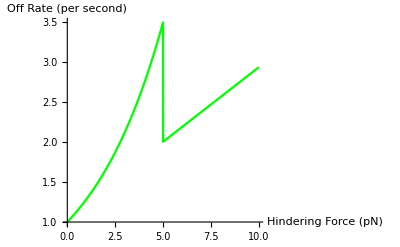

```mathematica
Plot[koff[f]/.Kparamvals,{f,0,10},AxesLabel->{"Hindering Force (pN)","Off Rate (per second)"},PlotStyle->Green]
```

but his velocity is the same as mine, so his run lengths are

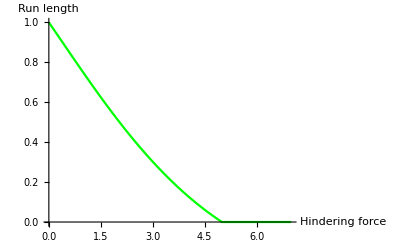

```mathematica
Krl=Plot[(dstep kstep[f])/koff[f]/.Kparamvals,{f,0,7},AxesLabel->{"Hindering force","Run length"},PlotStyle->Green]
```

Comparing to mine

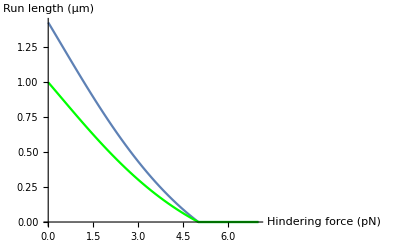

```mathematica
Show[{myrl,Krl}]
```

Unfortunately, neither Jing nor Michael have run lengths as a function of force that I can compare these to.